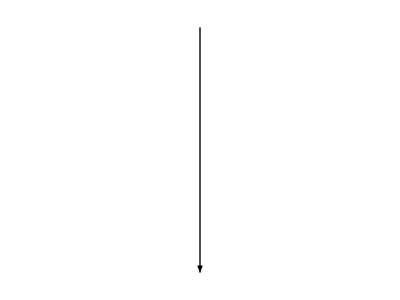
Orbifold Covering | Orbigraph Covering
-Graphics3D- | -Graphics-
-Graphics- | -Graphics-
-Graphics3D- | -Graphics-

```mathematica
sphere = RevolutionPlot3D[{Sqrt[1-t^2],t},{t,-1,1},{θ,0,2π},PlotStyle->Blue,Mesh->12, Axes->False,Boxed->False];
partSphere = RevolutionPlot3D[{Sqrt[1.04-t^2],t},{t,-1.04,1.05},{θ,-Pi/3+Pi/30,0},Mesh->{10,1},PlotStyle->Red, Axes->False,Boxed->False];

goodOrbi = {{0,1,3},{1,0,3},{2,2,0}};

cover = CreateFiniteCoveringGraph@goodOrbi;

goodOrbi = SetProperty[
AdjacencyOrbigraph@goodOrbi,
{
VertexSize->.1,
EdgeStyle->Directive[Thick, Black],
EdgeLabelStyle->20,
VertexStyle->
{
1 -> Red,
2-> Yellow,
3->Purple
}
}

];

Grid[
{
{
Style["Orbifold Covering", "Subsection",FontSize->Scaled[.030]],
Style["Orbigraph Covering", "Subsection",FontSize->Scaled[.030]]
},
{
Show[sphere,partSphere, ImageSize->Scaled[.4]],
SetProperty[cover,ImageSize->Scaled[.5]]
},
{
Item[
Graphics[{Arrowheads[.1],Arrow[{{0,.3},{0,-.3}}]}, ImageSize->Scaled[.3]],Alignment->Right
],
Item[
Graphics[{Arrowheads[.1],Arrow[{{0,.3},{0,-.3}}]}, ImageSize->Scaled[.3]],Alignment->Left
]
},
{
RevolutionPlot3D[{.5*(1-x^2),x},{x,-1,1},{θ,0,2π},Mesh->{5,10},PlotStyle->Blue,Axes->False,Boxed->False,ImageSize->Scaled[.3]],
SetProperty[goodOrbi,ImageSize->Scaled[.5]]
}
},
Alignment->{
{Right, Left}
},
ItemSize->{{ Scaled[.5], Scaled[.5] }},
Spacings->{Scaled[.3],0}
]
```

## Good and Bad Orbifolds

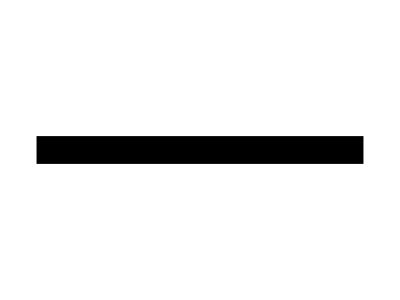
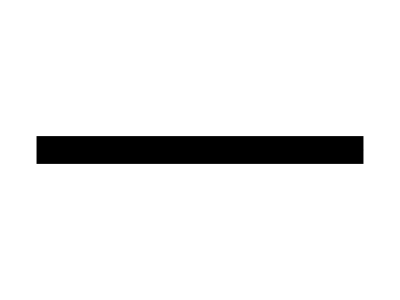
Infinite Cover |  | Orbifold |  | Finite Cover
-Graphics3D- | -Graphics- | -Graphics3D- | -Graphics- | -Graphics3D-
-Graphics3D- | -Graphics- | -Graphics3D- | -Graphics- | ×

```mathematica
teardrop=Piecewise[{{1/Sqrt[3]*x,x≤Sqrt[3]},{Sqrt[4/3-(x-4/Sqrt[3])^2],Sqrt[3]<x≤2*Sqrt[3]}}];
cone=RevolutionPlot3D[{teardrop,-x},{x,0,1},{θ,0,2π},Mesh->{5,10},PlotRange->{{-2,2},{-2,2},{-4,0}},PlotStyle->Red];
bulb=RevolutionPlot3D[{teardrop,-x},{x,1,2Sqrt[3]},{θ,0,2π},Mesh->{10,10},PlotRange->{{-2,2},{-2,2},{-4,0}},Exclusions->None,PlotStyle->Blue];


football = RevolutionPlot3D[{.5*(1-x^2),x},{x,-1,1},{θ,0,2π},Mesh->{5,10},PlotStyle->Blue,Axes->False];

sphere = RevolutionPlot3D[{Sqrt[1-t^2],t},{t,-1,1},{θ,0,2π},PlotStyle->Blue, Axes->False];

f[x_, y_] := Piecewise[
{
{Sqrt[(1-y)*.4*(1 - 1/(1-y)^2 x^2)], y >= 0},
{Sqrt[(1+y)*.4*(1 - 1/(1+y)^2 x^2)], y < 0}

}
]
t = Plot3D[f[x,y], {x, -1,1},{y,-1,1}, AxesLabel->{x,y, z},Axes->False,Boxed->False,PlotStyle->Blue, Exclusions->None];
b =  Plot3D[-f[x,y], {x, -1,1},{y,-1,1}, AxesLabel->{x,y, z}, Axes->False,Boxed->False, PlotStyle->Blue,Exclusions->None];




planeBig = Plot3D[1 ,{x,-1,1}, {y,-1,1}, PlotStyle->Green, Mesh-> {4,4}, Axes->False, Boxed->False,RegionFunction->Function[{x,y,z}, -1/5≥  x ||x ≥  1/5 ||  -1/5 ≥ y|| y ≥ 1/5]];
planeSmall = Plot3D[ 1,{x, -1/5, 1/5}, {y, -1/5, 1/5} ,PlotStyle->Blue,Axes->False, Boxed->False,Mesh->0];



Grid[
{
{
Style["Infinite Cover", "Subsection", FontSize->Scaled[.020]],
Spacer[1],
Style["Orbifold", "Subsection", FontSize->Scaled[.020]],
Spacer[1],
Style["Finite Cover", "Subsection", FontSize->Scaled[.020]]
},
{
Show[planeBig, planeSmall, ImageSize->Scaled[1.0]],
Graphics[{Arrowheads[.5],Thickness[.05],Arrow[{{.3,0},{-.3,0}}]}, ImageSize->Scaled[1.0]],
Show[t, b, PlotRange->{{-1,1},{-1,1}, {-1,1}},ImageSize->Scaled[1]],
Graphics[{Arrowheads[.5],Thickness[.05],Arrow[{{-.3,0},{.3,0}}]}, ImageSize->Scaled[1.0]],
RevolutionPlot3D[{3+Cos[t], Sin[t]}, {t, 0, 2Pi},Boxed->False, Axes->False,PlotStyle->Blue,BoundaryStyle->None, ImageSize->Scaled[1]]
},
{
Show[t, b, PlotRange->{{-1,1},{-1,1}, {-1,1}},ImageSize->Scaled[1]],
Graphics[{Arrowheads[.5],Thickness[.05],Arrow[{{.3,0},{-.3,0}}]}, ImageSize->Scaled[1.0]],
Show[bulb, cone, SphericalRegion->True,Axes->False,Boxed->False, ImageSize->Scaled[1]],
Graphics[{Arrowheads[.5],Thickness[.05],Arrow[{{-.3,0},{.3,0}}]}, ImageSize->Scaled[1.0]],
Magnify[Text[Style["×", Red,FontSize->Scaled[1], TextAlignment->Center]], 4]
}
},
Alignment->{
Center
},
ItemSize->{{ Scaled[.25], Scaled[.05],Scaled[.25], Scaled[.05], Scaled[.25] }},
Spacings->{Scaled[.01],Scaled[.05]},
Frame->All
]
```

## Covering Graphs and Quotients

```mathematica
grassman1=PermutationGroup[{
Cycles[{{1,2},{3,4}}],
Cycles[{{1,3},{2,4}}],
Cycles[{{1,4},{2,3}}]
}];
cover=CompleteGraph[6,VertexSize->0.3, VertexLabels->Table[i -> i, {i, 1, 6}]];

cover = SetProperty[cover, VertexLabelStyle->15];

highlightCover = HighlightGraph[cover, CompletePartition[cover, GroupOrbits[grassman1]]];
highlightCover =SetProperty[highlightCover, 
{
VertexStyle->{
1->Red,
2->Red,
3->Red,
4->Red,
5->Yellow,
6->Purple
},
VertexShapeFunction->{
1->"Square",
2->"Square",
3->"Square",
4->"Square",
5->"Triangle",
6->"Star"}
}
];

orbigraph1=OrbigraphFromGroup[cover, grassman1];
orbigraph1 = SetProperty[orbigraph1, 
{
VertexSize->.2,
VertexShapeFunction-> {1->"Square", 2-> "Triangle", 3->"Star"}, 
VertexStyle->{1-> Red, 2->Yellow, 3->Purple},
EdgeLabelStyle->15,
VertexLabelStyle->15
}
];

Column[{
PaneSelector[
{
1 -> Style["What is a covering graph?","Subsection", FontSize->Scaled[.020]],
2-> Style["What is an equitable partition?", "Subsection", FontSize->Scaled[.020]], 
3-> Style["How do we quotient?","Subsection", FontSize->Scaled[.020]]
},
Dynamic[time],
TransitionEffect->"Fade",
 Alignment->Center],
Slider[Dynamic[time], {1, 3, 1}],
PaneSelector[
{
1 -> SetProperty[cover,ImageSize->Scaled[.2]],
2-> SetProperty[highlightCover,ImageSize->Scaled[.2]] ,
3-> Grid[
{
{
SetProperty[highlightCover, ImageSize->Scaled[.2]], 
SetProperty[orbigraph1, ImageSize->Scaled[.2]]
}
}, 
Spacings->{Scaled[.1], 0},
ItemSize->Full]
},
Dynamic[time],
ImageSize->Full, 
TransitionEffect->"Fade",
 Alignment->Center]
},Center]
```

```mathematica
dwnArrw = {Arrowheads[.1],Arrow[{{0,0},{0,-.5}}]};

badOrbi = SetProperty[
AdjacencyOrbigraph[{{0,2,1},{1,0,2},{2,1,0}}],
{
VertexSize -> .2,
VertexStyle->
{
1 -> Red,
2-> Yellow,
3->Purple
},
EdgeLabelStyle -> 15,
VertexShapeFunction->
{
1-> "Triangle",
2->"Square",
3->"Star"
},
ImageSize->Scaled[.4]
}
];

goodOrbi = SetProperty[
AdjacencyOrbigraph[{{0,3},{1,2}}],
{
VertexSize->.2,
EdgeLabelStyle -> 15,
VertexStyle->
{
1-> Red, 
2-> Yellow
},
 VertexShapeFunction->
{
1-> "Triangle", 
2-> "Square"
},
ImageSize->Scaled[.4]
}
];

goodCover = SetProperty[CreateFiniteCoveringGraph[Normal@WeightedAdjacencyMatrix@goodOrbi],
ImageSize->Scaled[.4]];



goodUCover = SetProperty[CreateUniversalCovering[goodOrbi,4], {VertexSize->.3,
ImageSize->Scaled[.4]}];
badUCover = SetProperty[CreateUniversalCovering[badOrbi,4], {VertexSize->.3,
ImageSize->Scaled[.4]}];

showcover = False;

Grid[
{
{
Style["Good Orbigraph", "Subsection", FontSize-> Scaled[.02]],
Style["Bad Orbigraph", "Subsection", FontSize->Scaled[.02]]
},
{
PaneSelector[{
False -> Checkbox[Dynamic[showcover]],
True -> goodUCover
},
Dynamic[showcover],
Alignment->Center
],
PaneSelector[{
True -> badUCover
},
Dynamic[showcover],
Alignment->Center
]
},
{
PaneSelector[{
True -> Graphics[dwnArrw,ImageSize->Scaled[.3]]
},
Dynamic[showcover],
Alignment->Center
],
PaneSelector[{
True -> Graphics[dwnArrw,ImageSize->Scaled[.3]]
},
Dynamic[showcover],
Alignment->Center
]
},
{
goodCover,
Magnify[Text[Style["  𝓍", Red, FontSize->Scaled[.2]]], 4]
},
{
Graphics[dwnArrw,ImageSize->Scaled[.3]],
Graphics[dwnArrw,ImageSize->Scaled[.3]]
},
{
goodOrbi,
badOrbi
}
},
Alignment->{{Right, Left}},
Spacings->{Scaled[.2], Scaled[.01]},
Background->{White, {{2,1}->Red}},
ItemSize->{{ Scaled[.5], Scaled[.5]}}
]
```

Good Orbigraph | Bad Orbigraph
 | 
 | 
-Graphics- |   𝓍
-Graphics- | -Graphics-
-Graphics- | -Graphics-

## Universal Covering Tree

```mathematica
sizes = SetProperty[CreateUniversalCovering[orbigraph1, #], VertexSize-> .2] &/@ Range[3];

GraphPlotRange[graph_Graph] := With[{embedding = GraphEmbedding@graph},
{{Min[First /@ embedding]-1, Max[First/@embedding]+1},{Min[Last/@embedding]-1, Max[Last/@embedding]+1}}]

Grid[{
{
SetProperty[orbigraph1,{EdgeLabelStyle->20,ImageSize->Scaled[.5]}],
ListAnimate[sizes, DefaultDuration->3, ImageSize->{Scaled[.5], Scaled[.5]}]
}
},
Alignment-> {{Right, Left}},
ItemSize->{{ Scaled[.5], Scaled[.5 ]}},
Spacings->{Scaled[.1], 0}
]
```

-Graphics- |

## Characterization of Good and Bad Orbigraphs

Good: only “balanced” cycles

Bad: at least one “unbalanced” cycle

```mathematica
badOrbi = SetProperty[
AdjacencyOrbigraph[{{0,3,1},{1,0,3},{3,1,0}}],
{
VertexSize -> .1,
EdgeStyle->Directive[Thick, Black],
EdgeLabelStyle->20,
VertexStyle->
{
1 -> Red,
2-> Yellow,
3->Purple
},
VertexShapeFunction->
{
1-> "Triangle",
2->"Square",
3->"Star"
}
}
];

goodOrbi = SetProperty[
AdjacencyOrbigraph[{{0,1,3},{1,0,3},{2,2,0}}],
{
VertexSize->.1,
EdgeStyle->Directive[Thick, Black],
EdgeLabelStyle->20,
VertexStyle->
{
1 -> Red,
2-> Yellow,
3->Purple
},
VertexShapeFunction->
{
1-> "Triangle",
2->"Square",
3->"Star"
}
}
];

dwnArrw = Graphics[{Arrowheads[.1],Arrow[{{0,.3},{0,-.3}}]}];

edgesToHighlight = {
{{}, Green},
{1->2, Green},
{2->3, Green},
{3->1,Green},
{1->3,Red},
{3->2,Red},
{2->1,Red}
};

textFrames = {
{"", "Subsection"},
{"3", "Subsection"},
{"3×3", "Subsection"},
{"3×3×3", "Subsection"},
{"3×3×3≠1", "Subsection"},
{"3×3×3≠1×1", "Subsection"},
{"3×3×3≠1×1×1", "Subsection"}
};

edgesToHighlight2 = {
{{}, Green},
{1->2,Green},
{2->3,Green},
{3->1,Green},
{1->3,Red},
{3->2,Red},
{2->1,Red}
};

textFrames2= {
{"", "Subsection"},
{"1", "Subsection"},
{"1×3", "Subsection"},
{"1×3×2", "Subsection"},
{"1×3×2=3", "Subsection"},
{"1×3×2=3×2", "Subsection"},
{"1×3×2=3×2×1", "Subsection"}
};




Grid[
{
{
Style["Good Orbigraph", "Subsection",FontSize->Scaled[.02], TextAlignment->Center],
Pane[Style["Bad Orbigraph", "Subsection",FontSize->Scaled[.02]], Scaled[.5]]
},
{
Manipulate[
Column[{
SetProperty[
HighlightGraph[goodOrbi,
Style[
First@edgesToHighlight2⟦#⟧,
Directive[Last@edgesToHighlight2⟦#⟧, Thick]
]&/@Range[d]
], ImageSize->Scaled[.5]],

Style[
First@textFrames2⟦d⟧,
Last@textFrames2⟦d⟧,
FontSize->Scaled[.020]
]
}
],

 {d, 1, 7,1}],
Manipulate[
Column[{
SetProperty[
HighlightGraph[badOrbi,
Style[
First@edgesToHighlight⟦#⟧,
Directive[Last@edgesToHighlight⟦#⟧, Thick]
]&/@Range[d]
],
ImageSize->Scaled[.5]],

Style[
First@textFrames⟦d⟧,
Last@textFrames⟦d⟧,
FontSize->Scaled[.02]
]
}
],
 {d, 1, 7,1}]
}
},
Alignment-> {{Right, Left}},
ItemSize->{{ Scaled[.5], Scaled[.5 ]}},
Spacings->{Scaled[.1], Scaled[.01]}
]
```

Good Orbigraph | Bad Orbigraph
 |

## Example: Good Orbigraph

```mathematica
GenerateRandomReversibleOrbigraph[n_, k_] := Module[{randOrbi = GenerateRandomOrbigraph[n, k], tries=0},
While[tries ≤ 400 && Not[ConnectedOrbigraphQ[randOrbi]] || Not[OrbigraphReversibleQ[randOrbi]],
randOrbi = GenerateRandomOrbigraph[n, k];
tries++;
];
Return[randOrbi];
]

randOrbi = Style["Nothing", "Subsubsection",FontSize->Scaled[.015]];
coveringGraph = Style["Nothing", "Subsubsection", FontSize->Scaled[.015]];

Grid[{
{
Button["Random Orbigraph", 
Dynamic[
coveringGraph = Style["Nothing", "Subsubsection"];
randOrbi = GenerateRandomReversibleOrbigraph[3,3];

randOrbi = SetProperty[
AdjacencyOrbigraph@randOrbi,
{
VertexSize->.3,
ImageSize->Scaled[.3],
EdgeLabelStyle->15,
VertexStyle->
{
1-> Red, 
2-> Yellow,
3->Purple
},
 VertexShapeFunction->
{
1-> "Triangle", 
2-> "Square",
3->"Star"
}
}
]
],
ImageSize->Scaled[.4]
]
},
{
Button["Finite Covering",
Dynamic[coveringGraph = SetProperty[
CreateFiniteCoveringGraph[WeightedAdjacencyMatrix@randOrbi],
{ImageSize->Scaled[.4], GraphLayout->"SpringEmbedding"}
];
],
ImageSize->Scaled[.2]
]
},
{
Dynamic[coveringGraph]
},
{
Item[ Graphics[{Arrowheads[.1],Arrow[{{0,.3},{0,-.3}}]}, ImageSize->Scaled[.2]],Alignment->Center]
},
{
Dynamic[randOrbi]
}
},
Alignment-> Center,
ItemSize->{{Scaled[1]}},
Spacings->{Scaled[.1], Scaled[.01]}
]
```

Random Orbigraph
Finite Covering

-Graphics-

## How did we discover and prove this connection?

Comes from Markov chain property “reversibility”

Reversible Markov chains satisfy the detailed balance equations: π_i P_(i, j)= π_j P_(j,i)

```mathematica
rightArrw = Graphics[{Arrowheads[.1],Arrow[{{-1.5,0},{1.5,0}}]}];
shortRightArrw = Graphics[{Arrowheads[.1],Arrow[{{0,0},{.3,0}}]}];

ro ={{0,2,1},{3,0,0},{2,0,1}};
P = ro/3;

markovChain = MarkovProcessFromOrbigraph@ro;

ro = SetProperty[
AdjacencyOrbigraph@ro,
{
ImageSize->Scaled[.3],
VertexSize->.1,
VertexStyle->
{
1-> Red, 
2-> Yellow,
3->Purple
},
 VertexShapeFunction->
{
1-> "Triangle", 
2-> "Square",
3->"Star"
}
}
];

totalCounts = 0;

GenerateRandomWalk[chain_DiscreteMarkovProcess, len_Integer] :=Module[{counts ,walk= {}, cur=1,next,i,  G = Graph@chain, T=Normal@MarkovProcessProperties[chain, "TransitionMatrix"]},
cur = RandomChoice[VertexList@G];
counts = {ConstantArray[0, VertexCount@G]};

 For[i = 0, i < len, i++, 
next = RandomChoice[Cases[T⟦cur⟧, x_/;x ≠ 0]-> Flatten[Position[T⟦cur⟧, x_/;x ≠ 0],1]];
walk = Append[walk, next];
counts = Append[counts, Last@counts];
counts⟦Length@counts,next⟧++; 
cur = next;
];

Return[{walk, counts}];
]


w = GenerateRandomWalk[markovChain, 5000];


Manipulate[
Grid[
{
{
HighlightGraph[
SetProperty[
ro, {
EdgeWeight-> N[PropertyValue[ro, EdgeWeight]/3],
EdgeLabelStyle-> 10,
EdgeStyle->Medium, 
VertexSize->.3,
ImageSize->Scaled[1.0]
}
]
, {Style[(First@w)⟦t⟧, Lighter@Pink]}],
Column[{
Style[StringJoin@{"π = [",Riffle[ToString@NumberForm[#,{2,2}]&/@N[(Last@w)⟦t⟧/t],", ", 2], "]"}, "Subsubsection",FontSize->Scaled[.02]],
Style[StringJoin@{"Steps: ",ToString@t}, "Subsubsection",FontSize->Scaled[.015]]
}
]
},
{
Grid[
{
{
Style["π_1P_(1, 2) = π_2P_(2, 1)", "Subsubsection",FontSize->Scaled[.02]],Style["π_1P_(1, 3) = π_3P_(3, 1)", "Subsubsection",FontSize->Scaled[.02]]
},
{
Style[StringJoin@{
ToString@NumberForm[If[t ≥ 4500, .31, P⟦1,2⟧ * N[(Last@w)⟦t⟧/t]⟦1⟧],{2,2}],
" = ", 
ToString@NumberForm[If[t ≥ 4500, .31, P⟦2,1⟧ * N[(Last@w)⟦t⟧/t]⟦2⟧],{2,2}]
},
"Subsubsection",FontSize->Scaled[.02]],
Style[StringJoin@{
ToString@NumberForm[If[t ≥ 4500, .16, P⟦1,3⟧ * N[(Last@w)⟦t⟧/t]⟦1⟧],{2,2}],
" = ", 
ToString@NumberForm[If[ t ≥ 4500, .16, P⟦3,1⟧ * N[(Last@w)⟦t⟧/t]⟦3⟧],{2,2}]
},
"Subsubsection",
FontSize->Scaled[.02]]
}
},
Frame->All,
Spacings->{3,1},
Alignment->Center
],
Style[MatrixForm[Normal[WeightedAdjacencyMatrix[ro]] / 3], "Subsubsection",FontSize->Scaled[.02]]
}

},
Alignment-> Center,
ItemSize->{{Scaled[.50], Scaled[.50]}}
],
{t, 1, Length@First@w, 1},
Alignment->Center
]
```

## Conclusion

Orbigraphs are graph theoretic analogues of Riemannian Orbifolds

We can distinguish good and bad orbigraphs

We can bound the number of singular points using the spectrum

## Acknowledgements

Dr. Liz Stanhope

Miller Foundation

Lewis & Clark College